# GHZ STATES - IBMQX2

## N = 2

In this section the data refers to the measurement of qubit 0, with the parameter ϕ = (π j)/(n+1) that changes from 0 to (π (2n+1))/(n+1).

THEORY

```mathematica
n=2;
phi[j_]:=(Pi j)/(n+1)
S[ϕ_]:=1/2(1+Cos[n*ϕ])
Subscript[list, th]=Table[S[phi[j]],{j,0,(2*n+1)}];
```

```mathematica
Subscript[x, axis]=Table[phi[j],{j,0,(2*n+1)}];
```

```mathematica
Length[Subscript[x, axis]]==Length[Subscript[list, th]]
```

True

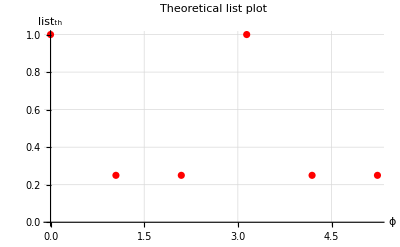

```mathematica
Subscript[listPlot, th]=ListPlot[Thread[{Subscript[x, axis],Subscript[list, th]}],AxesLabel->{HoldForm["ϕ"],HoldForm["list_th"]},PlotLabel->HoldForm["Theoretical list plot"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

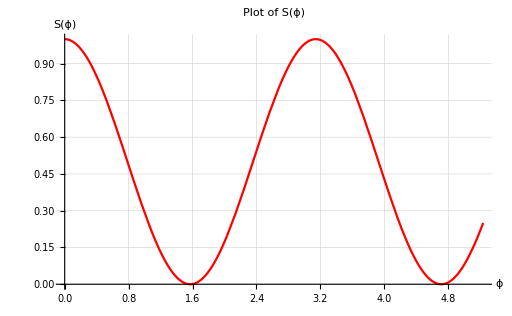

```mathematica
Subscript[plot, th]=Plot[S[ϕ],{ϕ,0,(Pi (2n+1))/(n+1)},AxesLabel->{HoldForm["ϕ"],HoldForm["S(ϕ)"]},PlotLabel->HoldForm["Plot of S(ϕ)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

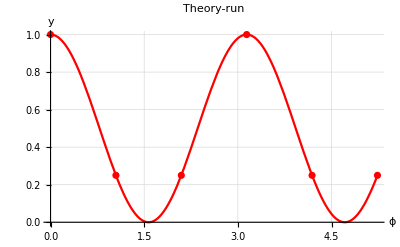

```mathematica
Show[Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, th]=Abs[N[Table[1/(2(n+1))*Sum[Exp[I  q phi[j]]*S[phi[j]],{j,0,(2*n+1)}],{q,-n,n}]]];
```

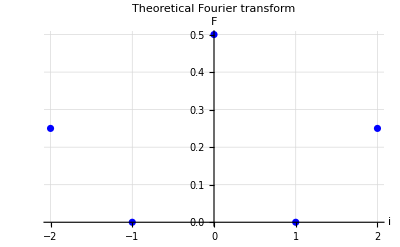

```mathematica
Subscript[FPlot, th]=ListPlot[Thread[{l,Subscript[F, th]}],AxesLabel->{HoldForm["i"],HoldForm["F"]},PlotLabel->HoldForm["Theoretical Fourier transform"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

SIMULATION

```mathematica
data1={1.0,0.2607421875,0.24609375,1.0,0.2529296875,0.2822265625};
```

#### Plot of the data choosen

```mathematica
simulation= data1
Length[simulation]
```

{1.,0.260742,0.246094,1.,0.25293,0.282227}

6

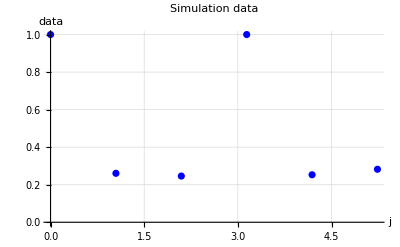

```mathematica
Subscript[plot, sim]=ListPlot[Thread[{Subscript[x, axis],simulation}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, sim]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*simulation[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

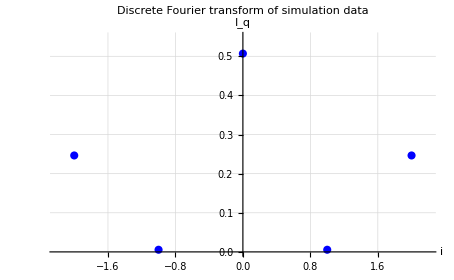

```mathematica
Subscript[I, sim]=Subscript[FPlot, sim]=ListPlot[Thread[{l,Subscript[F, sim]}],AxesLabel->{HoldForm["i"],HoldForm["I_q"]},PlotLabel->HoldForm["Discrete Fourier transform of simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{0,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

```mathematica
Lower=2 √(Subscript[F, sim][[Length[Subscript[F, sim]]]])
Upper=√(Subscript[F, sim][[n+1]]/2)+√(Subscript[F, sim][[Length[Subscript[F, sim]]]])
```

0.992995

0.999985

RUN

8192 shots

```mathematica
data1={0.8961181640625,0.3009033203125,0.2689208984375,0.904541015625,0.3109130859375,0.262939453125};
data2={0.8907470703125,0.2939453125,0.26904296875,0.8948974609375,0.3101806640625,0.2646484375};
data3={0.8997802734375,0.2940673828125,0.2628173828125,0.902587890625,0.299072265625,0.2606201171875};
```

#### Plot of the data choosen

```mathematica
run=data2  (*inserire il data che si vuole*)
Length[run]
```

{0.890747,0.293945,0.269043,0.894897,0.310181,0.264648}

6

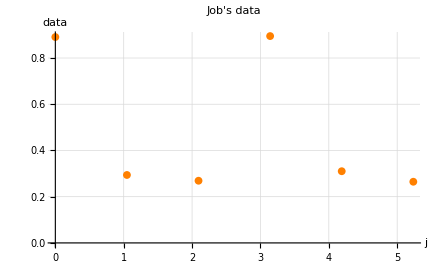

```mathematica
Subscript[plot, run]=ListPlot[Thread[{Subscript[x, axis],run}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Job's data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Orange}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, run]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*run[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

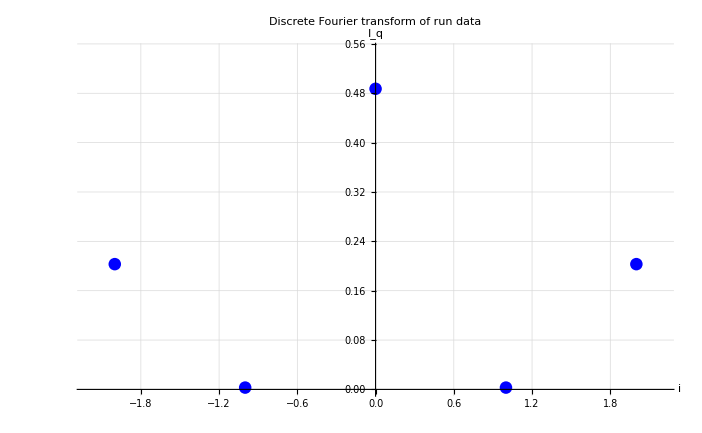

```mathematica
Subscript[I, run]=Subscript[FPlot, run]=ListPlot[Thread[{l,Subscript[F, run]}],AxesLabel->{HoldForm["i"],HoldForm["I_q"]},PlotLabel->HoldForm["Discrete Fourier transform of run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{0,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

Fidelity

```mathematica
F1=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data1[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}]
```

{0.205128,0.0027975,0.490723,0.0027975,0.205128}

```mathematica
F2=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data2[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

```mathematica
F3=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data3[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

```mathematica
F2Lower1= 2 √F1[[Length[F1]]]
F2Upper1=√(F1[[n+1]]/2)+√F1[[Length[F1]]]
```

0.905822

0.948251

```mathematica
F2Lower2= 2 √F2[[Length[F2]]]
F2Upper2=√(F2[[n+1]]/2)+√F2[[Length[F2]]]
```

0.901208

0.944185

```mathematica
F2Lower3= 2 √F3[[Length[F3]]]
F2Upper3=√(F3[[n+1]]/2)+√F3[[Length[F3]]]
```

0.911242

0.94882

COMPARE

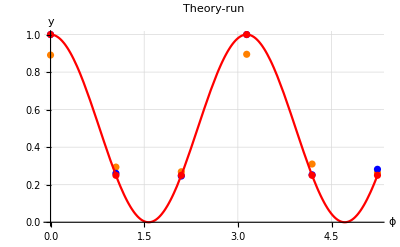

```mathematica
Show[Subscript[plot, run],Subscript[plot, sim],Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

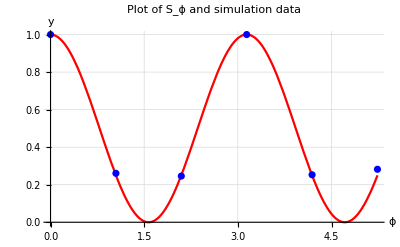

```mathematica
Subscript[S, sim]=Show[Subscript[plot, th],Subscript[plot, sim],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Plot of S_ϕ and simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

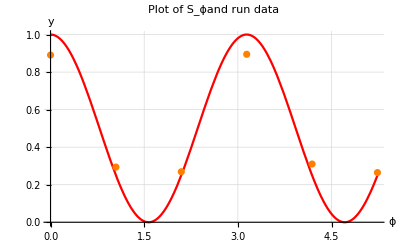

```mathematica
Subscript[S, run]=Show[Subscript[plot, th],Subscript[plot, run],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Plot of S_ϕand run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

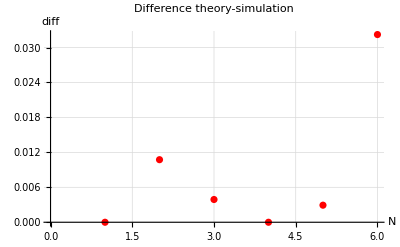

```mathematica
differenza=Abs[Subscript[list, th]-simulation];
ListPlot[differenza,AxesLabel->{HoldForm["N"],HoldForm["diff"]},PlotLabel->HoldForm["Difference theory-simulation"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

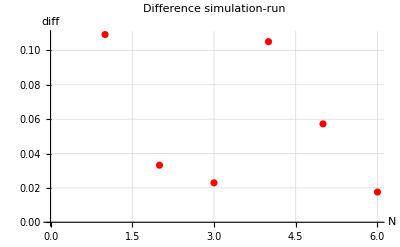

```mathematica
differenza=Abs[simulation-run];
ListPlot[differenza,AxesLabel->{HoldForm["N"],HoldForm["diff"]},PlotLabel->HoldForm["Difference simulation-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

Graphics to save

-Graphics-

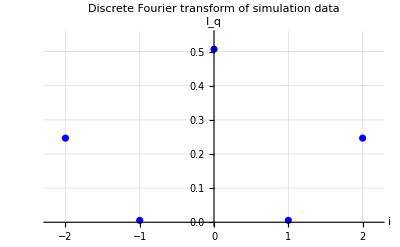

-Graphics-

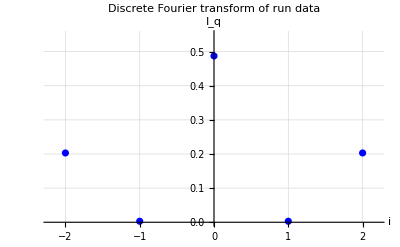

```mathematica
Subscript[S, sim]
Subscript[I, sim]
Subscript[S, run]
Subscript[I, run]
```

## N = 3

In this section the data refers to the measurement of qubit 0, with the parameter ϕ = (π j)/(n+1) that changes from 0 to (π (2n+1))/(n+1).

THEORY

```mathematica
n=3;
phi[j_]:=(Pi j)/(n+1)
S[ϕ_]:=1/2(1+Cos[n*ϕ])
Subscript[list, th]=Table[S[phi[j]],{j,0,(2*n+1)}];
```

```mathematica
Subscript[x, axis]=Table[phi[j],{j,0,(2*n+1)}];
```

```mathematica
Length[Subscript[x, axis]]==Length[Subscript[list, th]]
```

True

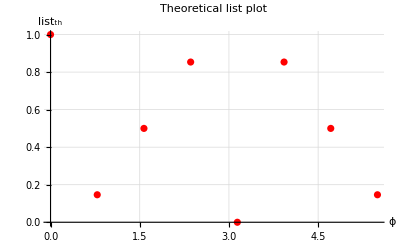

```mathematica
Subscript[listPlot, th]=ListPlot[Thread[{Subscript[x, axis],Subscript[list, th]}],AxesLabel->{HoldForm["ϕ"],HoldForm["list_th"]},PlotLabel->HoldForm["Theoretical list plot"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

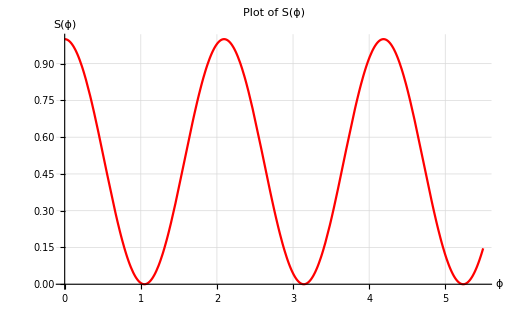

```mathematica
Subscript[plot, th]=Plot[S[ϕ],{ϕ,0,(Pi (2n+1))/(n+1)},AxesLabel->{HoldForm["ϕ"],HoldForm["S(ϕ)"]},PlotLabel->HoldForm["Plot of S(ϕ)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

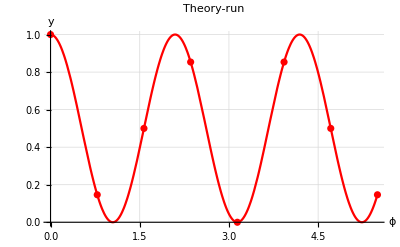

```mathematica
Show[Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, th]=Abs[N[Table[1/(2(n+1))*Sum[Exp[I  q phi[j]]*S[phi[j]],{j,0,(2*n+1)}],{q,-n,n}]]];
```

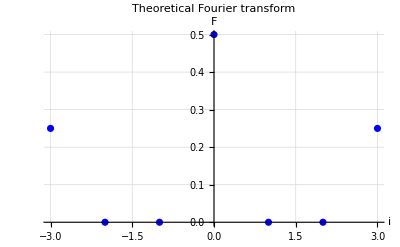

```mathematica
Subscript[FPlot, th]=ListPlot[Thread[{l,Subscript[F, th]}],AxesLabel->{HoldForm["i"],HoldForm["F"]},PlotLabel->HoldForm["Theoretical Fourier transform"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

SIMULATION

```mathematica
data1={1.0,0.1455078125,0.505859375,0.8623046875,0.0,0.8544921875,0.50390625,0.1396484375};
```

#### Plot of the data choosen

```mathematica
simulation= data1
Length[simulation]
```

{1.,0.145508,0.505859,0.862305,0.,0.854492,0.503906,0.139648}

8

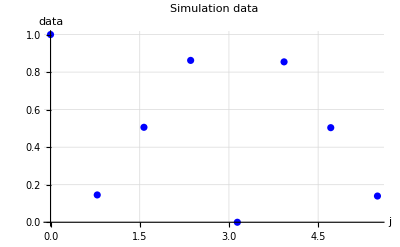

```mathematica
Subscript[plot, sim]=ListPlot[Thread[{Subscript[x, axis],simulation}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, sim]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*simulation[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

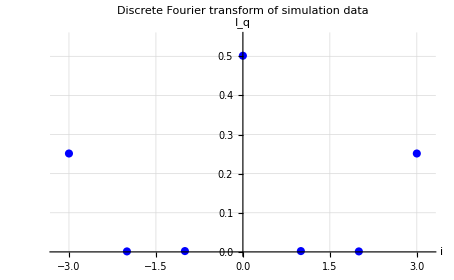

```mathematica
Subscript[I, sim]=Subscript[FPlot, sim]=ListPlot[Thread[{l,Subscript[F, sim]}],AxesLabel->{HoldForm["i"],HoldForm["I_q"]},PlotLabel->HoldForm["Discrete Fourier transform of simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{0,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

```mathematica
Lower=2 √(Subscript[F, sim][[Length[Subscript[F, sim]]]])
Upper=√(Subscript[F, sim][[n+1]]/2)+√(Subscript[F, sim][[Length[Subscript[F, sim]]]])
```

1.00308

1.00227

RUN

8192 shots

```mathematica
data1={0.693603515625,0.0887451171875,0.6724853515625,0.445068359375,0.173828125,0.725341796875,0.186279296875,0.45361328125};
data2={0.702880859375,0.093994140625,0.674072265625,0.458251953125,0.1685791015625,0.724853515625,0.178955078125,0.4473876953125};
data3 = {0.6881103515625,0.0906982421875,0.6614990234375,0.442626953125,0.1708984375,0.707763671875,0.1778564453125,0.4354248046875};
```

#### Plot of the data choosen

```mathematica
run=data2  (*inserire il data che si vuole*)
Length[run]
```

{0.702881,0.0939941,0.674072,0.458252,0.168579,0.724854,0.178955,0.447388}

8

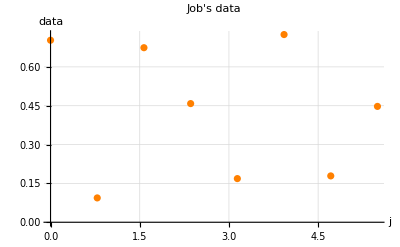

```mathematica
Subscript[plot, run]=ListPlot[Thread[{Subscript[x, axis],run}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Job's data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Orange}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, run]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*run[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

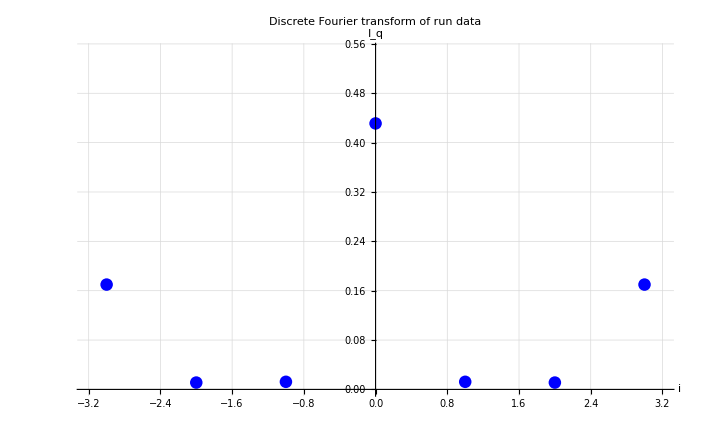

```mathematica
Subscript[I, run]=Subscript[FPlot, run]=ListPlot[Thread[{l,Subscript[F, run]}],AxesLabel->{HoldForm["i"],HoldForm["I_q"]},PlotLabel->HoldForm["Discrete Fourier transform of run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{0,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

Fidelity

```mathematica
F1=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data1[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}]
```

{0.168502,0.0106297,0.0101767,0.429871,0.0101767,0.0106297,0.168502}

```mathematica
F2=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data2[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

```mathematica
F3=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data3[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

```mathematica
F3Lower1= 2 √F1[[Length[F1]]]
F3Upper1=√(F1[[n+1]]/2)+√F1[[Length[F1]]]
```

0.820981

0.874102

```mathematica
F3Lower2= 2 √F2[[Length[F2]]]
F3Upper2=√(F2[[n+1]]/2)+√F2[[Length[F2]]]
```

0.824414

0.876492

```mathematica
F3Lower3= 2 √F3[[Length[F3]]]
F3Upper3=√(F3[[n+1]]/2)+√F3[[Length[F3]]]
```

0.813983

0.866263

COMPARE

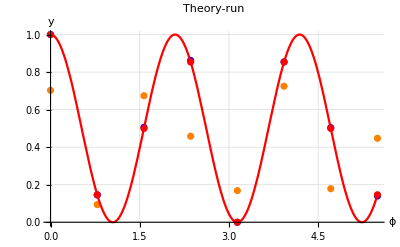

```mathematica
Show[Subscript[plot, run],Subscript[plot, sim],Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

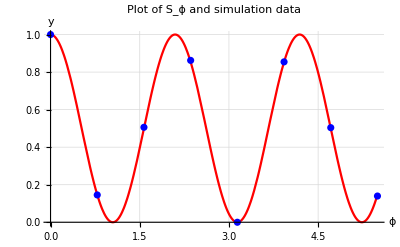

```mathematica
Subscript[S, sim]=Show[Subscript[plot, th],Subscript[plot, sim],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Plot of S_ϕ and simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

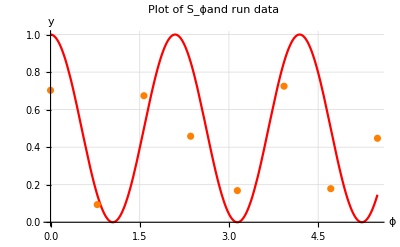

```mathematica
Subscript[S, run]=Show[Subscript[plot, th],Subscript[plot, run],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Plot of S_ϕand run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

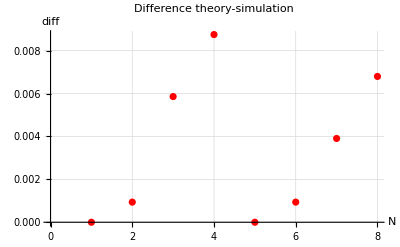

```mathematica
differenza=Abs[Subscript[list, th]-simulation];
ListPlot[differenza,AxesLabel->{HoldForm["N"],HoldForm["diff"]},PlotLabel->HoldForm["Difference theory-simulation"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

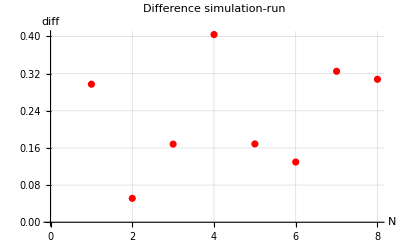

```mathematica
differenza=Abs[simulation-run];
ListPlot[differenza,AxesLabel->{HoldForm["N"],HoldForm["diff"]},PlotLabel->HoldForm["Difference simulation-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

Graphics to save

-Graphics-

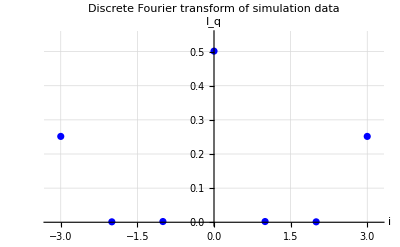

-Graphics-

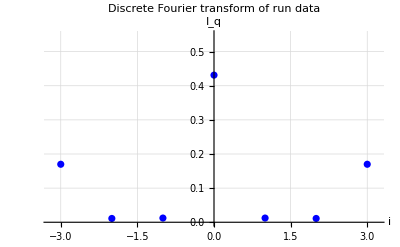

```mathematica
Subscript[S, sim]
Subscript[I, sim]
Subscript[S, run]
Subscript[I, run]
```

## N = 4

In this section the data refers to the measurement of qubit 0, with the parameter ϕ = (π j)/(n+1) that changes from 0 to (π (2n+1))/(n+1).

THEORY

```mathematica
n=4;
phi[j_]:=(Pi j)/(n+1)
S[ϕ_]:=1/2(1+Cos[n*ϕ])
Subscript[list, th]=Table[S[phi[j]],{j,0,(2*n+1)}];
```

```mathematica
Subscript[x, axis]=Table[phi[j],{j,0,(2*n+1)}];
```

```mathematica
Length[Subscript[x, axis]]==Length[Subscript[list, th]]
```

True

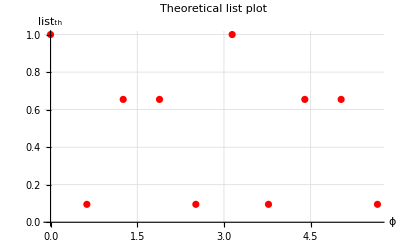

```mathematica
Subscript[listPlot, th]=ListPlot[Thread[{Subscript[x, axis],Subscript[list, th]}],AxesLabel->{HoldForm["ϕ"],HoldForm["list_th"]},PlotLabel->HoldForm["Theoretical list plot"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

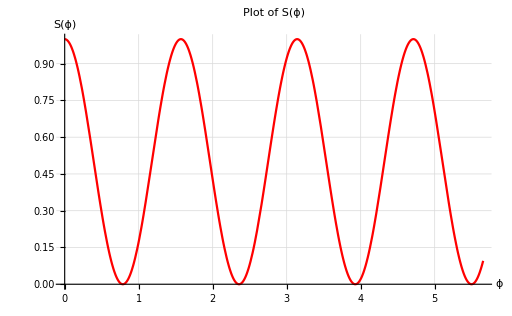

```mathematica
Subscript[plot, th]=Plot[S[ϕ],{ϕ,0,(Pi (2n+1))/(n+1)},AxesLabel->{HoldForm["ϕ"],HoldForm["S(ϕ)"]},PlotLabel->HoldForm["Plot of S(ϕ)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

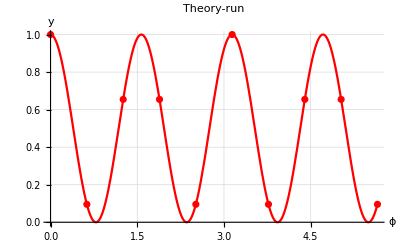

```mathematica
Show[Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, th]=Abs[N[Table[1/(2(n+1))*Sum[Exp[I  q phi[j]]*S[phi[j]],{j,0,(2*n+1)}],{q,-n,n}]]];
```

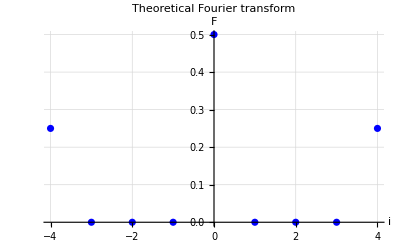

```mathematica
Subscript[FPlot, th]=ListPlot[Thread[{l,Subscript[F, th]}],AxesLabel->{HoldForm["i"],HoldForm["F"]},PlotLabel->HoldForm["Theoretical Fourier transform"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

SIMULATION

```mathematica
data1={1.0,0.0791015625,0.640625,0.6064453125,0.0986328125,1.0,0.0927734375,0.6787109375,0.6376953125,0.1044921875};
```

#### Plot of the data choosen

```mathematica
simulation= data1
Length[simulation]
```

{1.,0.0791016,0.640625,0.606445,0.0986328,1.,0.0927734,0.678711,0.637695,0.104492}

10

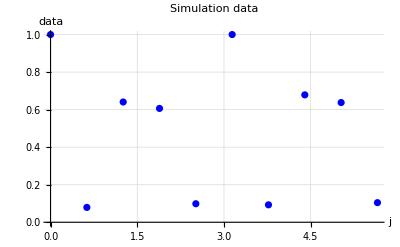

```mathematica
Subscript[plot, sim]=ListPlot[Thread[{Subscript[x, axis],simulation}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, sim]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*simulation[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

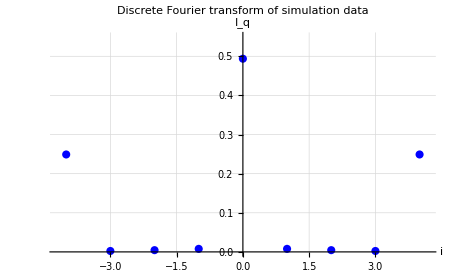

```mathematica
Subscript[I, sim]=Subscript[FPlot, sim]=ListPlot[Thread[{l,Subscript[F, sim]}],AxesLabel->{HoldForm["i"],HoldForm["I_q"]},PlotLabel->HoldForm["Discrete Fourier transform of simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{0,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

```mathematica
Lower=2 √(Subscript[F, sim][[Length[Subscript[F, sim]]]])
Upper=√(Subscript[F, sim][[n+1]]/2)+√(Subscript[F, sim][[Length[Subscript[F, sim]]]])
```

0.998078

0.995953

RUN

8192 shots

```mathematica
data1={0.144775390625,0.2696533203125,0.234375,0.200927734375,0.5067138671875,0.1510009765625,0.2532958984375,0.2392578125,0.226806640625,0.4862060546875};
data2={0.1533203125,0.27587890625,0.2430419921875,0.1982421875,0.490478515625,0.1668701171875,0.2401123046875,0.2308349609375,0.2061767578125,0.4554443359375};
(*data3 = {0.1376953125,0.28271484375,0.2425537109375,0.2027587890625,0.539794921875,0.139892578125,0.2608642578125,0.25146484375,0.205810546875,0.4854736328125};*)
data3 = {0.1256103515625,0.2626953125,0.19921875,0.22314453125,0.49267578125,0.1290283203125,0.25244140625,0.211669921875,0.231689453125,0.46728515625};
```

#### Plot of the data choosen

```mathematica
run=data1  (*inserire il data che si vuole*)
Length[run]
```

{0.144775,0.269653,0.234375,0.200928,0.506714,0.151001,0.253296,0.239258,0.226807,0.486206}

10

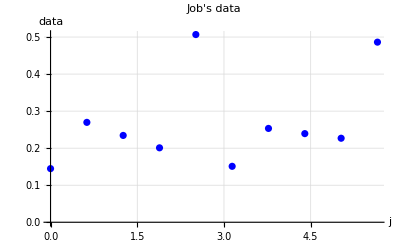

```mathematica
Subscript[plot, run]=ListPlot[Thread[{Subscript[x, axis],run}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Job's data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, run]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*run[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

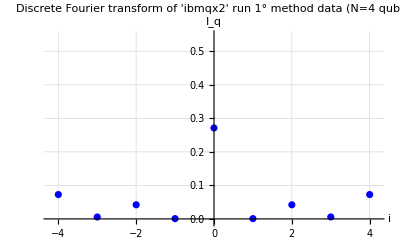

```mathematica
Subscript[I, run]=Subscript[FPlot, run]=ListPlot[Thread[{l,Subscript[F, run]}],AxesLabel->{Style["i",Black,FontFamily->"HoldForm",FontSize->16],Style["I_q",Black,FontFamily->"HoldForm",FontSize->16]} ,PlotLabel->HoldForm["Discrete Fourier transform of 'ibmqx2' run 1° method data (N=4 qubit)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{-0.01,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

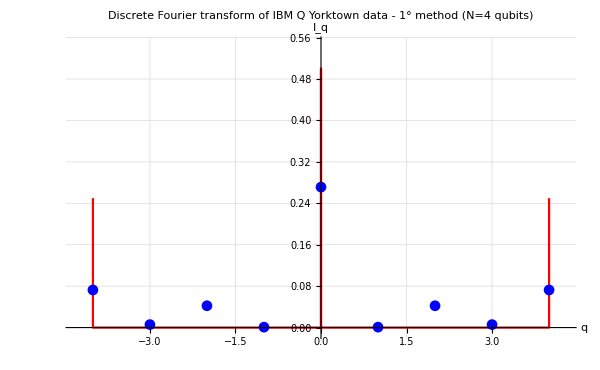

```mathematica
verticalSize=430;
orSize=600;
Fideale=Insert[Insert[Insert[Insert[Subscript[F, th],0,2],0,n+1+1],0,n+1+1+1+1],0,2n+1+1+1+1];
lideale=Insert[Insert[Insert[Insert[l,-n,2],0,n+1+1],0,n+1+1+1+1],n,2n+1+1+1+1];
FPlotideale=ListLinePlot[Thread[{lideale,Fideale}],AxesLabel->{Style["q",Black,FontFamily->"HoldForm",FontSize->16],Style["I_q",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Discrete Fourier transform of ideal simulation data (N=6 qubits)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{-0.01,0.55}}, PlotLegends->{},PlotStyle->{Red}];

Show[FPlotideale,Subscript[FPlot, run],AxesLabel->{Style["q",Black,FontFamily->"HoldForm",FontSize->16],Style["I_q",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Discrete Fourier transform of IBM Q Yorktown data - 1° method (N=4 qubits)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.3,n+0.3},{-0.01,0.55}}, PlotLegends->{},PlotStyle->{Red} ,ImageSize->{orSize,verticalSize}]
```

Fidelity

```mathematica
F1=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data1[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}]
```

{0.0726293,0.0057489,0.0421445,0.000819433,0.271301,0.000819433,0.0421445,0.0057489,0.0726293}

```mathematica
F2=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data2[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

```mathematica
F3=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data3[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

```mathematica
F4Lower1= 2 √F1[[Length[F1]]]
F4Upper1=√(F1[[n+1]]/2)+√F1[[Length[F1]]]
```

0.538996

0.637806

```mathematica
F4Lower2= 2 √F2[[Length[F2]]]
F4Upper2=√(F2[[n+1]]/2)+√F2[[Length[F2]]]
```

0.5183

0.623869

```mathematica
F4Lower3= 2 √F3[[Length[F3]]]
F4Upper3=√(F3[[n+1]]/2)+√F3[[Length[F3]]]
```

0.531507

0.625993

COMPARE

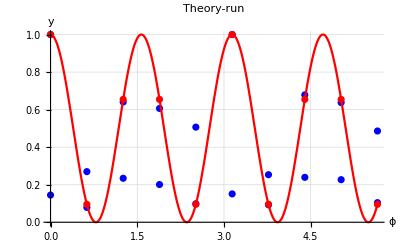

```mathematica
Show[Subscript[plot, run],Subscript[plot, sim],Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

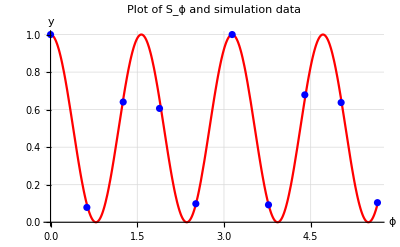

```mathematica
Subscript[S, sim]=Show[Subscript[plot, th],Subscript[plot, sim],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Plot of S_ϕ and simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

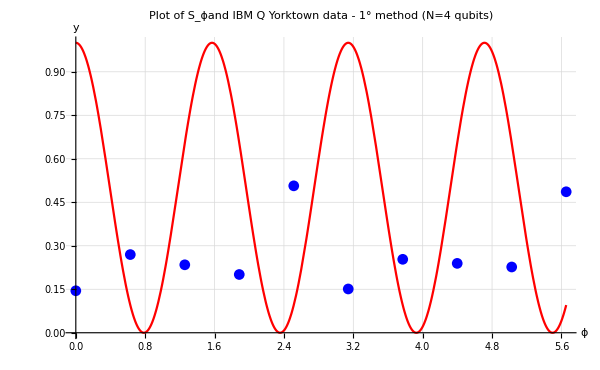

```mathematica
Subscript[S, run]=Show[Subscript[plot, th],Subscript[plot, run],AxesLabel->{Style["ϕ",Black,FontFamily->"HoldForm",FontSize->16],Style["y",Black,FontFamily->"HoldForm",FontSize->16]} ,PlotLabel->HoldForm["Plot of S_ϕand IBM Q Yorktown data - 1° method (N=4 qubits)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},ImageSize->{orSize,verticalSize}]
```

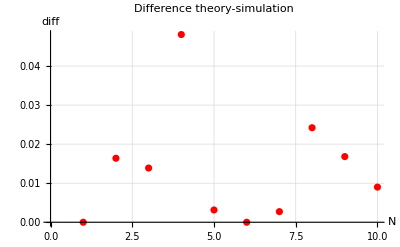

```mathematica
differenza=Abs[Subscript[list, th]-simulation];
ListPlot[differenza,AxesLabel->{HoldForm["N"],HoldForm["diff"]},PlotLabel->HoldForm["Difference theory-simulation"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

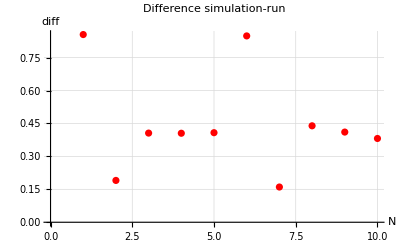

```mathematica
differenza=Abs[simulation-run];
ListPlot[differenza,AxesLabel->{HoldForm["N"],HoldForm["diff"]},PlotLabel->HoldForm["Difference simulation-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

Graphics to save

-Graphics-

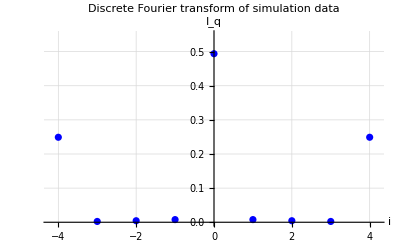

-Graphics-

-Graphics-

```mathematica
Subscript[S, sim]
Subscript[I, sim]
Subscript[S, run]
Subscript[I, run]
```

## N = 5

In this section the data refers to the measurement of qubit 0, with the parameter ϕ = (π j)/(n+1) that changes from 0 to (π (2n+1))/(n+1).

THEORY

```mathematica
n=5;
phi[j_]:=(Pi j)/(n+1)
S[ϕ_]:=1/2(1+Cos[n*ϕ])
Subscript[list, th]=Table[S[phi[j]],{j,0,(2*n+1)}];
```

```mathematica
Subscript[x, axis]=Table[phi[j],{j,0,(2*n+1)}];
```

```mathematica
Length[Subscript[x, axis]]==Length[Subscript[list, th]]
```

True

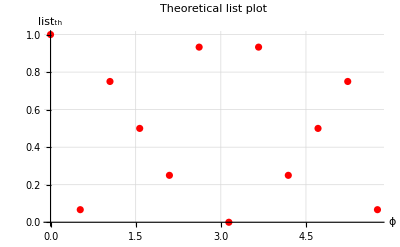

```mathematica
Subscript[listPlot, th]=ListPlot[Thread[{Subscript[x, axis],Subscript[list, th]}],AxesLabel->{HoldForm["ϕ"],HoldForm["list_th"]},PlotLabel->HoldForm["Theoretical list plot"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

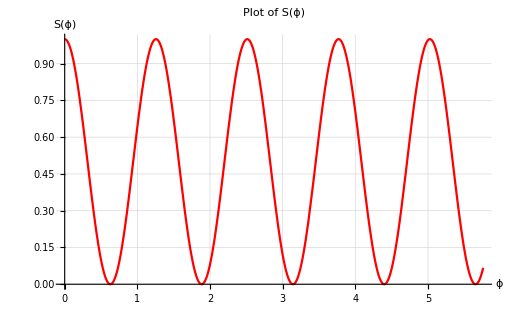

```mathematica
Subscript[plot, th]=Plot[S[ϕ],{ϕ,0,(Pi (2n+1))/(n+1)},AxesLabel->{HoldForm["ϕ"],HoldForm["S(ϕ)"]},PlotLabel->HoldForm["Plot of S(ϕ)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

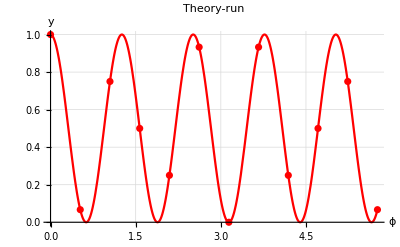

```mathematica
Show[Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, th]=Abs[N[Table[1/(2(n+1))*Sum[Exp[I  q phi[j]]*S[phi[j]],{j,0,(2*n+1)}],{q,-n,n}]]];
```

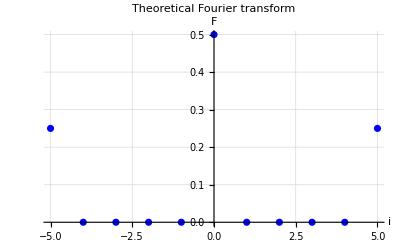

```mathematica
Subscript[FPlot, th]=ListPlot[Thread[{l,Subscript[F, th]}],AxesLabel->{HoldForm["i"],HoldForm["F"]},PlotLabel->HoldForm["Theoretical Fourier transform"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

SIMULATION

```mathematica
data1={1.0,0.0751953125,0.7353515625,0.5009765625,0.2568359375,0.943359375,0.0,0.9306640625,0.2421875,0.494140625,0.728515625,0.0595703125};
```

#### Plot of the data choosen

```mathematica
simulation= data1
Length[simulation]
```

{1.,0.0751953,0.735352,0.500977,0.256836,0.943359,0.,0.930664,0.242188,0.494141,0.728516,0.0595703}

12

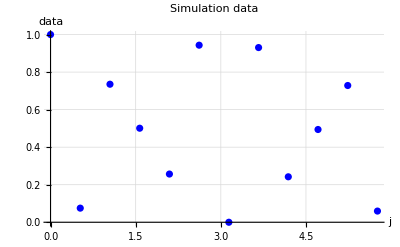

```mathematica
Subscript[plot, sim]=ListPlot[Thread[{Subscript[x, axis],simulation}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, sim]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*simulation[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

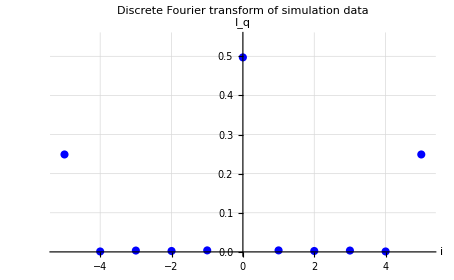

```mathematica
Subscript[I, sim]=Subscript[FPlot, sim]=ListPlot[Thread[{l,Subscript[F, sim]}],AxesLabel->{HoldForm["i"],HoldForm["I_q"]},PlotLabel->HoldForm["Discrete Fourier transform of simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{0,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

```mathematica
Lower=2 √(Subscript[F, sim][[Length[Subscript[F, sim]]]])
Upper=√(Subscript[F, sim][[n+1]]/2)+√(Subscript[F, sim][[Length[Subscript[F, sim]]]])
```

0.998109

0.997669

RUN

8192 shots

```mathematica
data1={0.166259765625,0.3048095703125,0.1309814453125,0.499267578125,0.31103515625,0.157958984375,0.2491455078125,0.1314697265625,0.277099609375,0.13720703125,0.3626708984375,0.247314453125};
data2={0.1790771484375,0.28662109375,0.136474609375,0.4984130859375,0.3096923828125,0.1551513671875,0.235595703125,0.138916015625,0.27783203125,0.151123046875,0.3680419921875,0.2489013671875};
data3 = {0.1839599609375,0.2884521484375,0.13623046875,0.470458984375,0.29345703125,0.1600341796875,0.2325439453125,0.1353759765625,0.2705078125,0.151611328125,0.34716796875,0.24462890625};
```

#### Plot of the data choosen

```mathematica
run=data2  (*inserire il data che si vuole*)
Length[run]
```

{0.179077,0.286621,0.136475,0.498413,0.309692,0.155151,0.235596,0.138916,0.277832,0.151123,0.368042,0.248901}

12

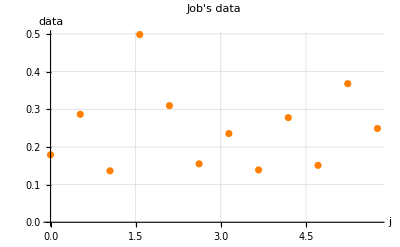

```mathematica
Subscript[plot, run]=ListPlot[Thread[{Subscript[x, axis],run}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Job's data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Orange}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, run]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*run[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

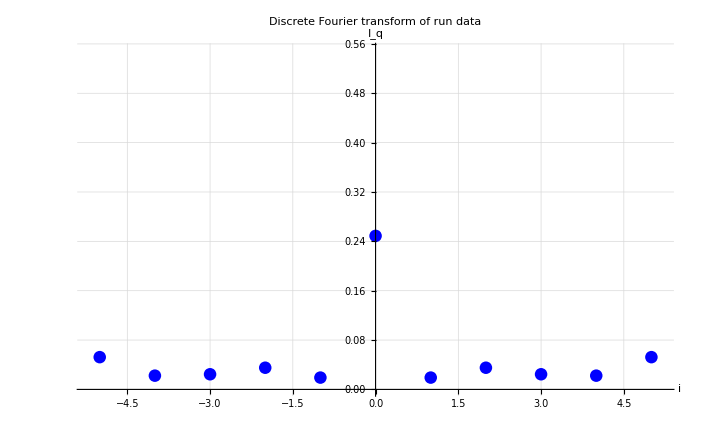

```mathematica
Subscript[I, run]=Subscript[FPlot, run]=ListPlot[Thread[{l,Subscript[F, run]}],AxesLabel->{HoldForm["i"],HoldForm["I_q"]},PlotLabel->HoldForm["Discrete Fourier transform of run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{0,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

Fidelity

```mathematica
F1=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data1[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}]
```

{0.0564507,0.0226891,0.0231932,0.0330921,0.0210281,0.247935,0.0210281,0.0330921,0.0231932,0.0226891,0.0564507}

```mathematica
F2=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data2[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

```mathematica
F3=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data3[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

```mathematica
F5Lower1= 2 √F1[[Length[F1]]]
F5Upper1=√(F1[[n+1]]/2)+√F1[[Length[F1]]]
```

0.475187

0.589684

```mathematica
F5Lower2= 2 √F2[[Length[F2]]]
F5Upper2=√(F2[[n+1]]/2)+√F2[[Length[F2]]]
```

0.457353

0.581395

```mathematica
F5Lower3= 2 √F3[[Length[F3]]]
F5Upper3=√(F3[[n+1]]/2)+√F3[[Length[F3]]]
```

0.44502

0.570985

COMPARE

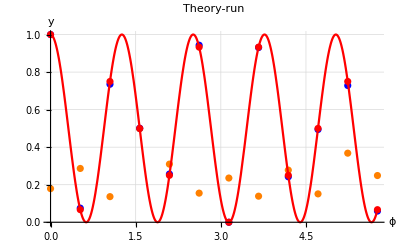

```mathematica
Show[Subscript[plot, run],Subscript[plot, sim],Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

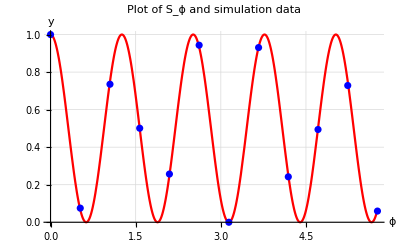

```mathematica
Subscript[S, sim]=Show[Subscript[plot, th],Subscript[plot, sim],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Plot of S_ϕ and simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

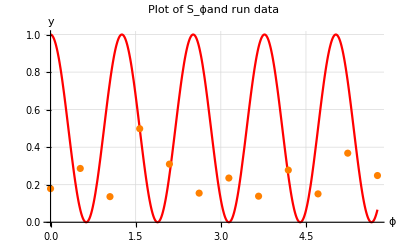

```mathematica
Subscript[S, run]=Show[Subscript[plot, th],Subscript[plot, run],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Plot of S_ϕand run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

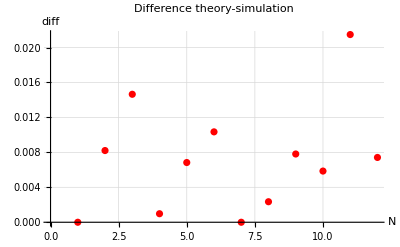

```mathematica
differenza=Abs[Subscript[list, th]-simulation];
ListPlot[differenza,AxesLabel->{HoldForm["N"],HoldForm["diff"]},PlotLabel->HoldForm["Difference theory-simulation"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

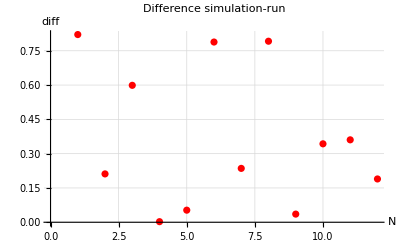

```mathematica
differenza=Abs[simulation-run];
ListPlot[differenza,AxesLabel->{HoldForm["N"],HoldForm["diff"]},PlotLabel->HoldForm["Difference simulation-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

Graphics to save

-Graphics-

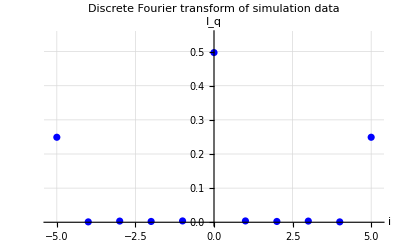

-Graphics-

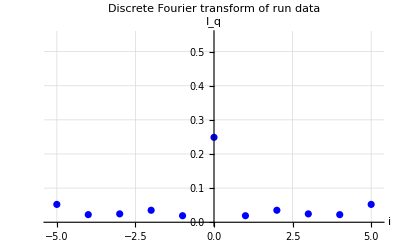

```mathematica
Subscript[S, sim]
Subscript[I, sim]
Subscript[S, run]
Subscript[I, run]
```

## Fidelity plot

No transpile:

```mathematica
VLower1={F2Lower1,F3Lower1,F4Lower1,F5Lower1}
VUpper1={F2Upper1,F3Upper1,F4Upper1,F5Upper1};
```

{0.905822,0.820981,0.538996,0.475187}

Transpile:

```mathematica
VLower2={F2Lower2,F3Lower2,F4Lower2,F5Lower2};
VUpper2={F2Upper2,F3Upper2,F4Upper2,F5Upper2};
```

Transpile user:

```mathematica
VLower3={F2Lower1,F3Lower1,F4Lower3,F5Lower1};
VUpper3={F2Upper1,F3Upper1,F4Upper3,F5Upper1};
```

```mathematica
qubits={2,3,4,5}
```

{2,3,4,5}

```mathematica
Thread[{qubits,VLower1}]
```

{{2,0.905822},{3,0.820981},{4,0.538996},{5,0.475187}}

```mathematica
retta=Plot[0.5,{x,0,5.5},PlotStyle->{Dashing[Tiny],Dashing[Large],Black}];
```

```mathematica
P1L=ListPlot[Thread[{qubits,VLower1}],AxesLabel->{Style["N",Black,FontFamily->"HoldForm",FontSize->16],Style["Fidelity",Black,FontFamily->"HoldForm",FontSize->16]},LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->{{2,3,4,5},Automatic} ,TicksStyle->Medium,GridLines->{{2,3,4,5},Automatic} , PlotRange->{{1.5,5.5},{0,1}}, PlotLegends->{},PlotStyle->{Green}];

P1U=ListPlot[Thread[{qubits,VUpper1}],AxesLabel->{Style["N",Black,FontFamily->"HoldForm",FontSize->16],Style["Fidelity",Black,FontFamily->"HoldForm",FontSize->16]},LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->{{2,3,4,5},Automatic} ,TicksStyle->Medium, GridLines->{{2,3,4,5},Automatic} ,  PlotRange->{{1.5,5.5},{0,1}}, PlotLegends->{},PlotStyle->{Orange}];

P2L=ListPlot[Thread[{qubits,VLower2}],AxesLabel->{Style["N",Black,FontFamily->"HoldForm",FontSize->16],Style["Fidelity",Black,FontFamily->"HoldForm",FontSize->16]},LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{1.5,5.5},{0,1}}, PlotLegends->{},PlotStyle->{Green}];
P2U=ListPlot[Thread[{qubits,VUpper2}],AxesLabel->{Style["N",Black,FontFamily->"HoldForm",FontSize->16],Style["Fidelity",Black,FontFamily->"HoldForm",FontSize->16]},LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium,GridLines->{{2,3,4,5},Automatic},  PlotRange->{{1.5,5.5},{0,1}}, PlotLegends->{},PlotStyle->{Orange}];

P3L=ListPlot[Thread[{qubits,VLower3}],AxesLabel->{Style["N",Black,FontFamily->"HoldForm",FontSize->16],Style["Fidelity",Black,FontFamily->"HoldForm",FontSize->16]},LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} ,  Ticks->{{2,3,4,5},Automatic} ,TicksStyle->Medium, GridLines->{{2,3,4,5},Automatic} , PlotRange->{{1.5,5.5},{0,1}}, PlotLegends->{},PlotStyle->{Green}];

P3U=ListPlot[Thread[{qubits,VUpper3}],AxesLabel->{Style["N",Black,FontFamily->"HoldForm",FontSize->16],Style["Fidelity",Black,FontFamily->"HoldForm",FontSize->16]},LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->{{2,3,4,5},Automatic} ,TicksStyle->Medium,GridLines->{{2,3,4,5},Automatic},  PlotRange->{{1.5,5.5},{0,1}}, PlotLegends->{},PlotStyle->{Orange}];
```

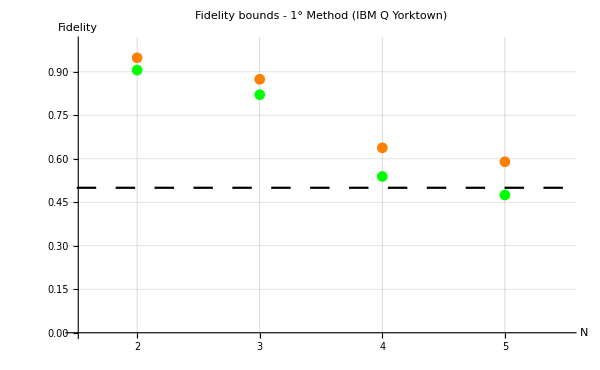

```mathematica
a=Show[P1L,P1U,retta,AxesLabel->{Style["N",Black,FontFamily->"HoldForm",FontSize->16],Style["Fidelity",Black,FontFamily->"HoldForm",FontSize->16]},LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->{{2,3,4,5},Automatic} ,TicksStyle->Medium,GridLines->{{2,3,4,5},Automatic}, PlotRange->{{1.5,5.5},{0,1}}, PlotLegends->{},PlotStyle->{Blue},PlotLabel->HoldForm["Fidelity bounds - 1° Method (IBM Q Yorktown)"],ImageSize->{orSize,verticalSize}]
```

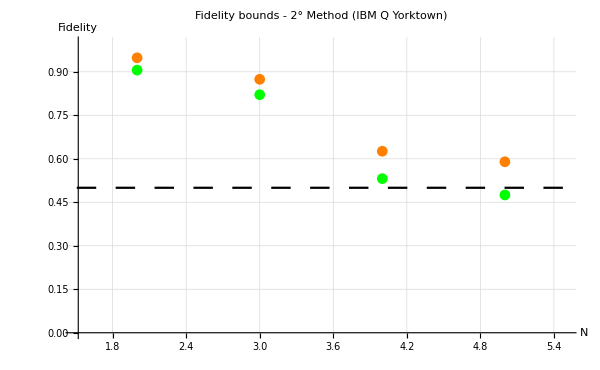

```mathematica
m=Show[P3L,P3U,retta,AxesLabel->{Style["N",Black,FontFamily->"HoldForm",FontSize->16],Style["Fidelity",Black,FontFamily->"HoldForm",FontSize->16]},LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{1.5,5.5},{0,1}}, PlotLegends->{},PlotStyle->{Blue},PlotLabel->HoldForm["Fidelity bounds - 2° Method (IBM Q Yorktown)"],ImageSize->{orSize,verticalSize}]
```

```mathematica
Show[r,m,a,ImageSize->{orSize,verticalSize}]
```

Show::gcomb: Could not combine the graphics objects in ….

Show[r,-Graphics-,-Graphics-,ImageSize→{600,430}]